# Ataque a la Kasiski

IMPORTANTE: REPASAR CIFRADO VIGENERE Y CRIPTOANÁLISIS DE KASISKI

En este documento vamos a resolver el siguiente ejercicio: El siguiente texto está cifrado por el método de Vigenère. Descifrarlo.
M.DRJB¡CKAJDWPWCÑYVKRRJUYNZHJDEDJU¡URQWC.DVDV.JCNRVÑKBVHWCJDXÑKCVRVD!AWP¡D¡BKDET RVVÑ¡LLJÑCCQÑYH!YGC¡D¡CUÑVYRQWCVRVD!AWPMÑXDJPGPJRC JQ¡ÑJÑCWKAVT RVÑÑNWÑMRVHWN¡ÑJÑCOKNDLKNCDJEGÑ ¡LDNNKXJVDDPRECKAJRS.U!JYWCUDQCNRVÑKN!HJ MHJRECÑYCDJÑJGRÑVDWC¡CÑYVD!ÑVGÑB H!CWC.RVDZÑ.RHÑMPJ,WUKNYRVOWWRAVORN!L!Z¡CÑZHHX.VYRREHJÑVORNDHWC¡C.DVYRB RWNLHWÑQAHLV,MDWPN.VSYQJHJQGUVVJCM.ECÑB¡C.D¡QYN¡PJ MHJÑYDLÑVHUNKRXÑJ

En primer lugar vamos  a definir nuestro mensaje es:

```mathematica
mensajecifrado="M.DRJB¡CKAJDWPWCÑYVKRRJUYNZHJDEDJU¡URQWC.DVDV.JCNRVÑKBVHWCJDXÑKCVRVD!AWP¡D¡BKDET RVVÑ¡LLJÑCCQÑYH!YGC¡D¡CUÑVYRQWCVRVD!AWPMÑXDJPGPJRC JQ¡ÑJÑCWKAVT RVÑÑNWÑMRVHWN¡ÑJÑCOKNDLKNCDJEGÑ ¡LDNNKXJVDDPRECKAJRS.U!JYWCUDQCNRVÑKN!HJ MHJRECÑYCDJÑJGRÑVDWC¡CÑYVD!ÑVGÑB H!CWC.RVDZÑ.RHÑMPJ,WUKNYRVOWWRAVORN!L!Z¡CÑZHHX.VYRREHJÑVORNDHWC¡C.DVYRB RWNLHWÑQAHLV,MDWPN.VSYQJHJQGUVVJCM.ECÑB¡C.D¡QYN¡PJ MHJÑYDLÑVHUNKRXÑJ "
```

M.DRJB¡CKAJDWPWCÑYVKRRJUYNZHJDEDJU¡URQWC.DVDV.JCNRVÑKBVHWCJDXÑKCVRVD!AWP¡D¡BKDET RVVÑ¡LLJÑCCQÑYH!YGC¡D¡CUÑVYRQWCVRVD!AWPMÑXDJPGPJRC JQ¡ÑJÑCWKAVT RVÑÑNWÑMRVHWN¡ÑJÑCOKNDLKNCDJEGÑ ¡LDNNKXJVDDPRECKAJRS.U!JYWCUDQCNRVÑKN!HJ MHJRECÑYCDJÑJGRÑVDWC¡CÑYVD!ÑVGÑB H!CWC.RVDZÑ.RHÑMPJ,WUKNYRVOWWRAVORN!L!Z¡CÑZHHX.VYRREHJÑVORNDHWC¡C.DVYRB RWNLHWÑQAHLV,MDWPN.VSYQJHJQGUVVJCM.ECÑB¡C.D¡QYN¡PJ MHJÑYDLÑVHUNKRXÑJ

Ahora vamos a definir nuestro alfabeto que será !., ABCDEFGHIJKLMNÑOPQRTSUVWXYZ¡

!., ABCDEFGHIJKLMNÑOPQRSTUVWXYZ¡

```mathematica
alf=StringJoin[Union[Characters[ StringJoin["ABCDEFGHIJKLMNÑOPQRSTUVWXYZ", mensajecifrado]]]]
```

!., ABCDEFGHIJKLMNÑOPQRSTUVWXYZ¡

```mathematica
M=Length[alf]
```

32

El ataque a la Kasiski consiste en lo siguiente:
1) Separamos el texto en digramas y trigramas
2) Estudiamos los digramas y trigramas que están repetidos y anotamos su distancia
3)La distancia entre cada uno de estos digramas y trigramas PUEDE ser un un múltiplo de la longitud de la clave de cifrado. Para ello vamos a definir las funciones que nos devuelven los diagramas y los triagramas. Queremos muchas coincidencias. Podríamos considerar también tetragramas y pentagramas, pero en este ejemplo nos restringiremos únicamente al caso de digramas y trigramas.
4) Cuando se halle la longitud de la clave de cifrado dividimos el texto recibido en grupos de ese tamaño y realizamos un análisis de frecuencia.

```mathematica
todosdigrafos=Table[Characters[mensajecifrado][[Range[k,k+1]]],{k,Length[Characters[mensajecifrado]]-2}]
```

{{M,.},{.,D},{D,R},{R,J},{J,B},{B,¡},{¡,C},{C,K},{K,A},{A,J},{J,D},{D,W},{W,P},{P,W},{W,C},{C,Ñ},{Ñ,Y},{Y,V},{V,K},{K,R},{R,R},{R,J},{J,U},{U,Y},{Y,N},{N,Z},{Z,H},{H,J},{J,D},{D,E},{E,D},{D,J},{J,U},{U,¡},{¡,U},{U,R},{R,Q},{Q,W},{W,C},{C,.},{.,D},{D,V},{V,D},{D,V},{V,.},{.,J},{J,C},{C,N},{N,R},{R,V},{V,Ñ},{Ñ,K},{K,B},{B,V},{V,H},{H,W},{W,C},{C,J},{J,D},{D,X},{X,Ñ},{Ñ,K},{K,C},{C,V},{V,R},{R,V},{V,D},{D,!},{!,A},{A,W},{W,P},{P,¡},{¡,D},{D,¡},{¡,B},{B,K},{K,D},{D,E},{E,T},{T, },{ ,R},{R,V},{V,V},{V,Ñ},{Ñ,¡},{¡,L},{L,L},{L,J},{J,Ñ},{Ñ,C},{C,C},{C,Q},{Q,Ñ},{Ñ,Y},{Y,H},{H,!},{!,Y},{Y,G},{G,C},{C,¡},{¡,D},{D,¡},{¡,C},{C,U},{U,Ñ},{Ñ,V},{V,Y},{Y,R},{R,Q},{Q,W},{W,C},{C,V},{V,R},{R,V},{V,D},{D,!},{!,A},{A,W},{W,P},{P,M},{M,Ñ},{Ñ,X},{X,D},{D,J},{J,P},{P,G},{G,P},{P,J},{J,R},{R,C},{C, },{ ,J},{J,Q},{Q,¡},{¡,Ñ},{Ñ,J},{J,Ñ},{Ñ,C},{C,W},{W,K},{K,A},{A,V},{V,T},{T, },{ ,R},{R,V},{V,Ñ},{Ñ,Ñ},{Ñ,N},{N,W},{W,Ñ},{Ñ,M},{M,R},{R,V},{V,H},{H,W},{W,N},{N,¡},{¡,Ñ},{Ñ,J},{J,Ñ},{Ñ,C},{C,O},{O,K},{K,N},{N,D},{D,L},{L,K},{K,N},{N,C},{C,D},{D,J},{J,E},{E,G},{G,Ñ},{Ñ, },{ ,¡},{¡,L},{L,D},{D,N},{N,N},{N,K},{K,X},{X,J},{J,V},{V,D},{D,D},{D,P},{P,R},{R,E},{E,C},{C,K},{K,A},{A,J},{J,R},{R,S},{S,.},{.,U},{U,!},{!,J},{J,Y},{Y,W},{W,C},{C,U},{U,D},{D,Q},{Q,C},{C,N},{N,R},{R,V},{V,Ñ},{Ñ,K},{K,N},{N,!},{!,H},{H,J},{J, },{ ,M},{M,H},{H,J},{J,R},{R,E},{E,C},{C,Ñ},{Ñ,Y},{Y,C},{C,D},{D,J},{J,Ñ},{Ñ,J},{J,G},{G,R},{R,Ñ},{Ñ,V},{V,D},{D,W},{W,C},{C,¡},{¡,C},{C,Ñ},{Ñ,Y},{Y,V},{V,D},{D,!},{!,Ñ},{Ñ,V},{V,G},{G,Ñ},{Ñ,B},{B, },{ ,H},{H,!},{!,C},{C,W},{W,C},{C,.},{.,R},{R,V},{V,D},{D,Z},{Z,Ñ},{Ñ,.},{.,R},{R,H},{H,Ñ},{Ñ,M},{M,P},{P,J},{J,,},{,,W},{W,U},{U,K},{K,N},{N,Y},{Y,R},{R,V},{V,O},{O,W},{W,W},{W,R},{R,A},{A,V},{V,O},{O,R},{R,N},{N,!},{!,L},{L,!},{!,Z},{Z,¡},{¡,C},{C,Ñ},{Ñ,Z},{Z,H},{H,H},{H,X},{X,.},{.,V},{V,Y},{Y,R},{R,R},{R,E},{E,H},{H,J},{J,Ñ},{Ñ,V},{V,O},{O,R},{R,N},{N,D},{D,H},{H,W},{W,C},{C,¡},{¡,C},{C,.},{.,D},{D,V},{V,Y},{Y,R},{R,B},{B, },{ ,R},{R,W},{W,N},{N,L},{L,H},{H,W},{W,Ñ},{Ñ,Q},{Q,A},{A,H},{H,L},{L,V},{V,,},{,,M},{M,D},{D,W},{W,P},{P,N},{N,.},{.,V},{V,S},{S,Y},{Y,Q},{Q,J},{J,H},{H,J},{J,Q},{Q,G},{G,U},{U,V},{V,V},{V,J},{J,C},{C,M},{M,.},{.,E},{E,C},{C,Ñ},{Ñ,B},{B,¡},{¡,C},{C,.},{.,D},{D,¡},{¡,Q},{Q,Y},{Y,N},{N,¡},{¡,P},{P,J},{J, },{ ,M},{M,H},{H,J},{J,Ñ},{Ñ,Y},{Y,D},{D,L},{L,Ñ},{Ñ,V},{V,H},{H,U},{U,N},{N,K},{K,R},{R,X},{X,Ñ},{Ñ,J}}

```mathematica
todostrigrafos=Table[Characters[mensajecifrado][[Range[k,k+2]]],{k,Length[Characters[mensajecifrado]]-2}]
```

{{M,.,D},{.,D,R},{D,R,J},{R,J,B},{J,B,¡},{B,¡,C},{¡,C,K},{C,K,A},{K,A,J},{A,J,D},{J,D,W},{D,W,P},{W,P,W},{P,W,C},{W,C,Ñ},{C,Ñ,Y},{Ñ,Y,V},{Y,V,K},{V,K,R},{K,R,R},{R,R,J},{R,J,U},{J,U,Y},{U,Y,N},{Y,N,Z},{N,Z,H},{Z,H,J},{H,J,D},{J,D,E},{D,E,D},{E,D,J},{D,J,U},{J,U,¡},{U,¡,U},{¡,U,R},{U,R,Q},{R,Q,W},{Q,W,C},{W,C,.},{C,.,D},{.,D,V},{D,V,D},{V,D,V},{D,V,.},{V,.,J},{.,J,C},{J,C,N},{C,N,R},{N,R,V},{R,V,Ñ},{V,Ñ,K},{Ñ,K,B},{K,B,V},{B,V,H},{V,H,W},{H,W,C},{W,C,J},{C,J,D},{J,D,X},{D,X,Ñ},{X,Ñ,K},{Ñ,K,C},{K,C,V},{C,V,R},{V,R,V},{R,V,D},{V,D,!},{D,!,A},{!,A,W},{A,W,P},{W,P,¡},{P,¡,D},{¡,D,¡},{D,¡,B},{¡,B,K},{B,K,D},{K,D,E},{D,E,T},{E,T, },{T, ,R},{ ,R,V},{R,V,V},{V,V,Ñ},{V,Ñ,¡},{Ñ,¡,L},{¡,L,L},{L,L,J},{L,J,Ñ},{J,Ñ,C},{Ñ,C,C},{C,C,Q},{C,Q,Ñ},{Q,Ñ,Y},{Ñ,Y,H},{Y,H,!},{H,!,Y},{!,Y,G},{Y,G,C},{G,C,¡},{C,¡,D},{¡,D,¡},{D,¡,C},{¡,C,U},{C,U,Ñ},{U,Ñ,V},{Ñ,V,Y},{V,Y,R},{Y,R,Q},{R,Q,W},{Q,W,C},{W,C,V},{C,V,R},{V,R,V},{R,V,D},{V,D,!},{D,!,A},{!,A,W},{A,W,P},{W,P,M},{P,M,Ñ},{M,Ñ,X},{Ñ,X,D},{X,D,J},{D,J,P},{J,P,G},{P,G,P},{G,P,J},{P,J,R},{J,R,C},{R,C, },{C, ,J},{ ,J,Q},{J,Q,¡},{Q,¡,Ñ},{¡,Ñ,J},{Ñ,J,Ñ},{J,Ñ,C},{Ñ,C,W},{C,W,K},{W,K,A},{K,A,V},{A,V,T},{V,T, },{T, ,R},{ ,R,V},{R,V,Ñ},{V,Ñ,Ñ},{Ñ,Ñ,N},{Ñ,N,W},{N,W,Ñ},{W,Ñ,M},{Ñ,M,R},{M,R,V},{R,V,H},{V,H,W},{H,W,N},{W,N,¡},{N,¡,Ñ},{¡,Ñ,J},{Ñ,J,Ñ},{J,Ñ,C},{Ñ,C,O},{C,O,K},{O,K,N},{K,N,D},{N,D,L},{D,L,K},{L,K,N},{K,N,C},{N,C,D},{C,D,J},{D,J,E},{J,E,G},{E,G,Ñ},{G,Ñ, },{Ñ, ,¡},{ ,¡,L},{¡,L,D},{L,D,N},{D,N,N},{N,N,K},{N,K,X},{K,X,J},{X,J,V},{J,V,D},{V,D,D},{D,D,P},{D,P,R},{P,R,E},{R,E,C},{E,C,K},{C,K,A},{K,A,J},{A,J,R},{J,R,S},{R,S,.},{S,.,U},{.,U,!},{U,!,J},{!,J,Y},{J,Y,W},{Y,W,C},{W,C,U},{C,U,D},{U,D,Q},{D,Q,C},{Q,C,N},{C,N,R},{N,R,V},{R,V,Ñ},{V,Ñ,K},{Ñ,K,N},{K,N,!},{N,!,H},{!,H,J},{H,J, },{J, ,M},{ ,M,H},{M,H,J},{H,J,R},{J,R,E},{R,E,C},{E,C,Ñ},{C,Ñ,Y},{Ñ,Y,C},{Y,C,D},{C,D,J},{D,J,Ñ},{J,Ñ,J},{Ñ,J,G},{J,G,R},{G,R,Ñ},{R,Ñ,V},{Ñ,V,D},{V,D,W},{D,W,C},{W,C,¡},{C,¡,C},{¡,C,Ñ},{C,Ñ,Y},{Ñ,Y,V},{Y,V,D},{V,D,!},{D,!,Ñ},{!,Ñ,V},{Ñ,V,G},{V,G,Ñ},{G,Ñ,B},{Ñ,B, },{B, ,H},{ ,H,!},{H,!,C},{!,C,W},{C,W,C},{W,C,.},{C,.,R},{.,R,V},{R,V,D},{V,D,Z},{D,Z,Ñ},{Z,Ñ,.},{Ñ,.,R},{.,R,H},{R,H,Ñ},{H,Ñ,M},{Ñ,M,P},{M,P,J},{P,J,,},{J,,,W},{,,W,U},{W,U,K},{U,K,N},{K,N,Y},{N,Y,R},{Y,R,V},{R,V,O},{V,O,W},{O,W,W},{W,W,R},{W,R,A},{R,A,V},{A,V,O},{V,O,R},{O,R,N},{R,N,!},{N,!,L},{!,L,!},{L,!,Z},{!,Z,¡},{Z,¡,C},{¡,C,Ñ},{C,Ñ,Z},{Ñ,Z,H},{Z,H,H},{H,H,X},{H,X,.},{X,.,V},{.,V,Y},{V,Y,R},{Y,R,R},{R,R,E},{R,E,H},{E,H,J},{H,J,Ñ},{J,Ñ,V},{Ñ,V,O},{V,O,R},{O,R,N},{R,N,D},{N,D,H},{D,H,W},{H,W,C},{W,C,¡},{C,¡,C},{¡,C,.},{C,.,D},{.,D,V},{D,V,Y},{V,Y,R},{Y,R,B},{R,B, },{B, ,R},{ ,R,W},{R,W,N},{W,N,L},{N,L,H},{L,H,W},{H,W,Ñ},{W,Ñ,Q},{Ñ,Q,A},{Q,A,H},{A,H,L},{H,L,V},{L,V,,},{V,,,M},{,,M,D},{M,D,W},{D,W,P},{W,P,N},{P,N,.},{N,.,V},{.,V,S},{V,S,Y},{S,Y,Q},{Y,Q,J},{Q,J,H},{J,H,J},{H,J,Q},{J,Q,G},{Q,G,U},{G,U,V},{U,V,V},{V,V,J},{V,J,C},{J,C,M},{C,M,.},{M,.,E},{.,E,C},{E,C,Ñ},{C,Ñ,B},{Ñ,B,¡},{B,¡,C},{¡,C,.},{C,.,D},{.,D,¡},{D,¡,Q},{¡,Q,Y},{Q,Y,N},{Y,N,¡},{N,¡,P},{¡,P,J},{P,J, },{J, ,M},{ ,M,H},{M,H,J},{H,J,Ñ},{J,Ñ,Y},{Ñ,Y,D},{Y,D,L},{D,L,Ñ},{L,Ñ,V},{Ñ,V,H},{V,H,U},{H,U,N},{U,N,K},{N,K,R},{K,R,X},{R,X,Ñ},{X,Ñ,J},{Ñ,J, }}

Con el comando Union conseguimos todos los digrafos y trigrafos que aparecen en el mensaje recibido

```mathematica
digrafos=Union[todosdigrafos]
```

{{!,A},{!,C},{!,H},{!,J},{!,L},{!,Ñ},{!,Y},{!,Z},{.,D},{.,E},{.,J},{.,R},{.,U},{.,V},{,,M},{,,W},{ ,H},{ ,J},{ ,M},{ ,R},{ ,¡},{A,H},{A,J},{A,V},{A,W},{B, },{B,K},{B,V},{B,¡},{C,.},{C, },{C,C},{C,D},{C,J},{C,K},{C,M},{C,N},{C,Ñ},{C,O},{C,Q},{C,U},{C,V},{C,W},{C,¡},{D,!},{D,D},{D,E},{D,H},{D,J},{D,L},{D,N},{D,P},{D,Q},{D,R},{D,V},{D,W},{D,X},{D,Z},{D,¡},{E,C},{E,D},{E,G},{E,H},{E,T},{G,C},{G,Ñ},{G,P},{G,R},{G,U},{H,!},{H,H},{H,J},{H,L},{H,Ñ},{H,U},{H,W},{H,X},{J,,},{J, },{J,B},{J,C},{J,D},{J,E},{J,G},{J,H},{J,Ñ},{J,P},{J,Q},{J,R},{J,U},{J,V},{J,Y},{K,A},{K,B},{K,C},{K,D},{K,N},{K,R},{K,X},{L,!},{L,D},{L,H},{L,J},{L,K},{L,L},{L,Ñ},{L,V},{M,.},{M,D},{M,H},{M,Ñ},{M,P},{M,R},{N,!},{N,.},{N,C},{N,D},{N,K},{N,L},{N,N},{N,R},{N,W},{N,Y},{N,Z},{N,¡},{Ñ,.},{Ñ, },{Ñ,B},{Ñ,C},{Ñ,J},{Ñ,K},{Ñ,M},{Ñ,N},{Ñ,Ñ},{Ñ,Q},{Ñ,V},{Ñ,X},{Ñ,Y},{Ñ,Z},{Ñ,¡},{O,K},{O,R},{O,W},{P,G},{P,J},{P,M},{P,N},{P,R},{P,W},{P,¡},{Q,A},{Q,C},{Q,G},{Q,J},{Q,Ñ},{Q,W},{Q,Y},{Q,¡},{R,A},{R,B},{R,C},{R,E},{R,H},{R,J},{R,N},{R,Ñ},{R,Q},{R,R},{R,S},{R,V},{R,W},{R,X},{S,.},{S,Y},{T, },{U,!},{U,D},{U,K},{U,N},{U,Ñ},{U,R},{U,V},{U,Y},{U,¡},{V,.},{V,,},{V,D},{V,G},{V,H},{V,J},{V,K},{V,Ñ},{V,O},{V,R},{V,S},{V,T},{V,V},{V,Y},{W,C},{W,K},{W,N},{W,Ñ},{W,P},{W,R},{W,U},{W,W},{X,.},{X,D},{X,J},{X,Ñ},{Y,C},{Y,D},{Y,G},{Y,H},{Y,N},{Y,Q},{Y,R},{Y,V},{Y,W},{Z,H},{Z,Ñ},{Z,¡},{¡,B},{¡,C},{¡,D},{¡,L},{¡,Ñ},{¡,P},{¡,Q},{¡,U}}

```mathematica
trigrafos=Union[todostrigrafos]
```

{{!,A,W},{!,C,W},{!,H,J},{!,J,Y},{!,L,!},{!,Ñ,V},{!,Y,G},{!,Z,¡},{.,D,R},{.,D,V},{.,D,¡},{.,E,C},{.,J,C},{.,R,H},{.,R,V},{.,U,!},{.,V,S},{.,V,Y},{,,M,D},{,,W,U},{ ,H,!},{ ,J,Q},{ ,M,H},{ ,R,V},{ ,R,W},{ ,¡,L},{A,H,L},{A,J,D},{A,J,R},{A,V,O},{A,V,T},{A,W,P},{B, ,H},{B, ,R},{B,K,D},{B,V,H},{B,¡,C},{C,.,D},{C,.,R},{C, ,J},{C,C,Q},{C,D,J},{C,J,D},{C,K,A},{C,M,.},{C,N,R},{C,Ñ,B},{C,Ñ,Y},{C,Ñ,Z},{C,O,K},{C,Q,Ñ},{C,U,D},{C,U,Ñ},{C,V,R},{C,W,C},{C,W,K},{C,¡,C},{C,¡,D},{D,!,A},{D,!,Ñ},{D,D,P},{D,E,D},{D,E,T},{D,H,W},{D,J,E},{D,J,Ñ},{D,J,P},{D,J,U},{D,L,K},{D,L,Ñ},{D,N,N},{D,P,R},{D,Q,C},{D,R,J},{D,V,.},{D,V,D},{D,V,Y},{D,W,C},{D,W,P},{D,X,Ñ},{D,Z,Ñ},{D,¡,B},{D,¡,C},{D,¡,Q},{E,C,K},{E,C,Ñ},{E,D,J},{E,G,Ñ},{E,H,J},{E,T, },{G,C,¡},{G,Ñ, },{G,Ñ,B},{G,P,J},{G,R,Ñ},{G,U,V},{H,!,C},{H,!,Y},{H,H,X},{H,J, },{H,J,D},{H,J,Ñ},{H,J,Q},{H,J,R},{H,L,V},{H,Ñ,M},{H,U,N},{H,W,C},{H,W,N},{H,W,Ñ},{H,X,.},{J,,,W},{J, ,M},{J,B,¡},{J,C,M},{J,C,N},{J,D,E},{J,D,W},{J,D,X},{J,E,G},{J,G,R},{J,H,J},{J,Ñ,C},{J,Ñ,J},{J,Ñ,V},{J,Ñ,Y},{J,P,G},{J,Q,G},{J,Q,¡},{J,R,C},{J,R,E},{J,R,S},{J,U,Y},{J,U,¡},{J,V,D},{J,Y,W},{K,A,J},{K,A,V},{K,B,V},{K,C,V},{K,D,E},{K,N,!},{K,N,C},{K,N,D},{K,N,Y},{K,R,R},{K,R,X},{K,X,J},{L,!,Z},{L,D,N},{L,H,W},{L,J,Ñ},{L,K,N},{L,L,J},{L,Ñ,V},{L,V,,},{M,.,D},{M,.,E},{M,D,W},{M,H,J},{M,Ñ,X},{M,P,J},{M,R,V},{N,!,H},{N,!,L},{N,.,V},{N,C,D},{N,D,H},{N,D,L},{N,K,R},{N,K,X},{N,L,H},{N,N,K},{N,R,V},{N,W,Ñ},{N,Y,R},{N,Z,H},{N,¡,Ñ},{N,¡,P},{Ñ,.,R},{Ñ, ,¡},{Ñ,B, },{Ñ,B,¡},{Ñ,C,C},{Ñ,C,O},{Ñ,C,W},{Ñ,J, },{Ñ,J,G},{Ñ,J,Ñ},{Ñ,K,B},{Ñ,K,C},{Ñ,K,N},{Ñ,M,P},{Ñ,M,R},{Ñ,N,W},{Ñ,Ñ,N},{Ñ,Q,A},{Ñ,V,D},{Ñ,V,G},{Ñ,V,H},{Ñ,V,O},{Ñ,V,Y},{Ñ,X,D},{Ñ,Y,C},{Ñ,Y,D},{Ñ,Y,H},{Ñ,Y,V},{Ñ,Z,H},{Ñ,¡,L},{O,K,N},{O,R,N},{O,W,W},{P,G,P},{P,J,,},{P,J, },{P,J,R},{P,M,Ñ},{P,N,.},{P,R,E},{P,W,C},{P,¡,D},{Q,A,H},{Q,C,N},{Q,G,U},{Q,J,H},{Q,Ñ,Y},{Q,W,C},{Q,Y,N},{Q,¡,Ñ},{R,A,V},{R,B, },{R,C, },{R,E,C},{R,E,H},{R,H,Ñ},{R,J,B},{R,J,U},{R,N,!},{R,N,D},{R,Ñ,V},{R,Q,W},{R,R,E},{R,R,J},{R,S,.},{R,V,D},{R,V,H},{R,V,Ñ},{R,V,O},{R,V,V},{R,W,N},{R,X,Ñ},{S,.,U},{S,Y,Q},{T, ,R},{U,!,J},{U,D,Q},{U,K,N},{U,N,K},{U,Ñ,V},{U,R,Q},{U,V,V},{U,Y,N},{U,¡,U},{V,.,J},{V,,,M},{V,D,!},{V,D,D},{V,D,V},{V,D,W},{V,D,Z},{V,G,Ñ},{V,H,U},{V,H,W},{V,J,C},{V,K,R},{V,Ñ,K},{V,Ñ,Ñ},{V,Ñ,¡},{V,O,R},{V,O,W},{V,R,V},{V,S,Y},{V,T, },{V,V,J},{V,V,Ñ},{V,Y,R},{W,C,.},{W,C,J},{W,C,Ñ},{W,C,U},{W,C,V},{W,C,¡},{W,K,A},{W,N,L},{W,N,¡},{W,Ñ,M},{W,Ñ,Q},{W,P,M},{W,P,N},{W,P,W},{W,P,¡},{W,R,A},{W,U,K},{W,W,R},{X,.,V},{X,D,J},{X,J,V},{X,Ñ,J},{X,Ñ,K},{Y,C,D},{Y,D,L},{Y,G,C},{Y,H,!},{Y,N,Z},{Y,N,¡},{Y,Q,J},{Y,R,B},{Y,R,Q},{Y,R,R},{Y,R,V},{Y,V,D},{Y,V,K},{Y,W,C},{Z,H,H},{Z,H,J},{Z,Ñ,.},{Z,¡,C},{¡,B,K},{¡,C,.},{¡,C,K},{¡,C,Ñ},{¡,C,U},{¡,D,¡},{¡,L,D},{¡,L,L},{¡,Ñ,J},{¡,P,J},{¡,Q,Y},{¡,U,R}}

A continuación, voy a ver que digrafos y trigrafos se repiten

```mathematica
frecuenciadi=Table[Count[todosdigrafos,digrafos[[k]]],{k,Length[digrafos]}]
```

{2,1,1,1,1,1,1,1,4,1,1,2,1,2,1,1,1,1,2,3,1,1,2,2,2,2,1,1,2,4,1,1,2,1,2,1,2,5,1,1,2,2,2,3,3,1,2,1,4,2,1,1,1,1,3,3,1,1,3,3,1,1,1,1,1,2,1,1,1,2,1,6,1,1,1,4,1,1,2,1,2,3,1,1,1,6,1,2,3,2,1,1,3,1,1,1,4,2,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,2,1,1,2,2,1,1,2,1,1,1,2,1,1,2,3,4,3,2,1,1,1,5,1,5,1,1,1,2,1,1,3,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,3,1,2,2,1,2,2,1,9,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,7,1,3,1,1,4,3,2,1,1,2,3,8,1,2,2,4,1,1,1,1,1,1,2,1,1,1,1,2,1,4,2,1,2,1,1,1,6,2,2,2,1,1,1}

```mathematica
frecuenciatri=Table[Count[todostrigrafos,trigrafos[[k]]],{k,Length[trigrafos]}]
```

{2,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,2,1,1,1,1,2,3,1,1,1,2,1,2,1,2,1,3,1,1,1,1,1,2,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,3,1,3,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,2,1,1,2,1,1,2,1,2,1,1,1,1,3,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,2,1,1,2,1,1,1}

```mathematica
Do[If[frecuenciadi[[k]]>1,Print[digrafos[[k]]," ocurre en la(s) posición(es) ",Flatten[Position[todosdigrafos,digrafos[[k]]]]," con distancia ",Differences[Flatten[Position[todosdigrafos,digrafos[[k]]]]]]],{k,Length[frecuenciadi]}]
```

{!,A} ocurre en la(s) posición(es) {69,117} con distancia {48}

{.,D} ocurre en la(s) posición(es) {2,41,317,365} con distancia {39,276,48}

{.,R} ocurre en la(s) posición(es) {257,263} con distancia {6}

{.,V} ocurre en la(s) posición(es) {298,342} con distancia {44}

{ ,M} ocurre en la(s) posición(es) {218,374} con distancia {156}

{ ,R} ocurre en la(s) posición(es) {81,145,323} con distancia {64,178}

{A,J} ocurre en la(s) posición(es) {10,194} con distancia {184}

{A,V} ocurre en la(s) posición(es) {142,282} con distancia {140}

{A,W} ocurre en la(s) posición(es) {70,118} con distancia {48}

{B, } ocurre en la(s) posición(es) {250,322} con distancia {72}

{B,¡} ocurre en la(s) posición(es) {6,362} con distancia {356}

{C,.} ocurre en la(s) posición(es) {40,256,316,364} con distancia {216,60,48}

{C,D} ocurre en la(s) posición(es) {171,227} con distancia {56}

{C,K} ocurre en la(s) posición(es) {8,192} con distancia {184}

{C,N} ocurre en la(s) posición(es) {48,208} con distancia {160}

{C,Ñ} ocurre en la(s) posición(es) {16,224,240,292,360} con distancia {208,16,52,68}

{C,U} ocurre en la(s) posición(es) {104,204} con distancia {100}

{C,V} ocurre en la(s) posición(es) {64,112} con distancia {48}

{C,W} ocurre en la(s) posición(es) {139,254} con distancia {115}

{C,¡} ocurre en la(s) posición(es) {100,238,314} con distancia {138,76}

{D,!} ocurre en la(s) posición(es) {68,116,244} con distancia {48,128}

{D,E} ocurre en la(s) posición(es) {30,78} con distancia {48}

{D,J} ocurre en la(s) posición(es) {32,124,172,228} con distancia {92,48,56}

{D,L} ocurre en la(s) posición(es) {167,380} con distancia {213}

{D,V} ocurre en la(s) posición(es) {42,44,318} con distancia {2,274}

{D,W} ocurre en la(s) posición(es) {12,236,338} con distancia {224,102}

{D,¡} ocurre en la(s) posición(es) {74,102,366} con distancia {28,264}

{E,C} ocurre en la(s) posición(es) {191,223,359} con distancia {32,136}

{G,Ñ} ocurre en la(s) posición(es) {175,248} con distancia {73}

{H,!} ocurre en la(s) posición(es) {96,252} con distancia {156}

{H,J} ocurre en la(s) posición(es) {28,216,220,304,348,376} con distancia {188,4,84,44,28}

{H,W} ocurre en la(s) posición(es) {56,156,312,328} con distancia {100,156,16}

{J, } ocurre en la(s) posición(es) {217,373} con distancia {156}

{J,C} ocurre en la(s) posición(es) {47,355} con distancia {308}

{J,D} ocurre en la(s) posición(es) {11,29,59} con distancia {18,30}

{J,Ñ} ocurre en la(s) posición(es) {89,137,161,229,305,377} con distancia {48,24,68,76,72}

{J,Q} ocurre en la(s) posición(es) {133,349} con distancia {216}

{J,R} ocurre en la(s) posición(es) {129,195,221} con distancia {66,26}

{J,U} ocurre en la(s) posición(es) {23,33} con distancia {10}

{K,A} ocurre en la(s) posición(es) {9,141,193} con distancia {132,52}

{K,N} ocurre en la(s) posición(es) {165,169,213,273} con distancia {4,44,60}

{K,R} ocurre en la(s) posición(es) {20,387} con distancia {367}

{M,.} ocurre en la(s) posición(es) {1,357} con distancia {356}

{M,H} ocurre en la(s) posición(es) {219,375} con distancia {156}

{N,!} ocurre en la(s) posición(es) {214,286} con distancia {72}

{N,D} ocurre en la(s) posición(es) {166,310} con distancia {144}

{N,K} ocurre en la(s) posición(es) {182,386} con distancia {204}

{N,R} ocurre en la(s) posición(es) {49,209} con distancia {160}

{N,¡} ocurre en la(s) posición(es) {158,370} con distancia {212}

{Ñ,B} ocurre en la(s) posición(es) {249,361} con distancia {112}

{Ñ,C} ocurre en la(s) posición(es) {90,138,162} con distancia {48,24}

{Ñ,J} ocurre en la(s) posición(es) {136,160,230,390} con distancia {24,70,160}

{Ñ,K} ocurre en la(s) posición(es) {52,62,212} con distancia {10,150}

{Ñ,M} ocurre en la(s) posición(es) {152,266} con distancia {114}

{Ñ,V} ocurre en la(s) posición(es) {106,234,246,306,382} con distancia {128,12,60,76}

{Ñ,Y} ocurre en la(s) posición(es) {17,94,225,241,378} con distancia {77,131,16,137}

{O,R} ocurre en la(s) posición(es) {284,308} con distancia {24}

{P,J} ocurre en la(s) posición(es) {128,268,372} con distancia {140,104}

{Q,W} ocurre en la(s) posición(es) {38,110} con distancia {72}

{R,E} ocurre en la(s) posición(es) {190,222,302} con distancia {32,80}

{R,J} ocurre en la(s) posición(es) {4,22} con distancia {18}

{R,N} ocurre en la(s) posición(es) {285,309} con distancia {24}

{R,Q} ocurre en la(s) posición(es) {37,109} con distancia {72}

{R,R} ocurre en la(s) posición(es) {21,301} con distancia {280}

{R,V} ocurre en la(s) posición(es) {50,66,82,114,146,154,210,258,276} con distancia {16,16,32,32,8,56,48,18}

{T, } ocurre en la(s) posición(es) {80,144} con distancia {64}

{V,D} ocurre en la(s) posición(es) {43,67,115,186,235,243,259} con distancia {24,48,71,49,8,16}

{V,H} ocurre en la(s) posición(es) {55,155,383} con distancia {100,228}

{V,Ñ} ocurre en la(s) posición(es) {51,84,147,211} con distancia {33,63,64}

{V,O} ocurre en la(s) posición(es) {277,283,307} con distancia {6,24}

{V,R} ocurre en la(s) posición(es) {65,113} con distancia {48}

{V,V} ocurre en la(s) posición(es) {83,353} con distancia {270}

{V,Y} ocurre en la(s) posición(es) {107,299,319} con distancia {192,20}

{W,C} ocurre en la(s) posición(es) {15,39,57,111,203,237,255,313} con distancia {24,18,54,92,34,18,58}

{W,N} ocurre en la(s) posición(es) {157,325} con distancia {168}

{W,Ñ} ocurre en la(s) posición(es) {151,329} con distancia {178}

{W,P} ocurre en la(s) posición(es) {13,71,119,339} con distancia {58,48,220}

{X,Ñ} ocurre en la(s) posición(es) {61,389} con distancia {328}

{Y,N} ocurre en la(s) posición(es) {25,369} con distancia {344}

{Y,R} ocurre en la(s) posición(es) {108,275,300,320} con distancia {167,25,20}

{Y,V} ocurre en la(s) posición(es) {18,242} con distancia {224}

{Z,H} ocurre en la(s) posición(es) {27,294} con distancia {267}

{¡,C} ocurre en la(s) posición(es) {7,103,239,291,315,363} con distancia {96,136,52,24,48}

{¡,D} ocurre en la(s) posición(es) {73,101} con distancia {28}

{¡,L} ocurre en la(s) posición(es) {86,178} con distancia {92}

{¡,Ñ} ocurre en la(s) posición(es) {135,159} con distancia {24}

```mathematica
Do[If[frecuenciatri[[k]]>1,Print[trigrafos[[k]]," ocurre en la(s) posición(es) ",Flatten[Position[todostrigrafos,trigrafos[[k]]]]," con distancia ",Differences[Flatten[Position[todostrigrafos,trigrafos[[k]]]]]]],{k,Length[frecuenciatri]}]
```

{!,A,W} ocurre en la(s) posición(es) {69,117} con distancia {48}

{.,D,V} ocurre en la(s) posición(es) {41,317} con distancia {276}

{ ,M,H} ocurre en la(s) posición(es) {218,374} con distancia {156}

{ ,R,V} ocurre en la(s) posición(es) {81,145} con distancia {64}

{A,W,P} ocurre en la(s) posición(es) {70,118} con distancia {48}

{B,¡,C} ocurre en la(s) posición(es) {6,362} con distancia {356}

{C,.,D} ocurre en la(s) posición(es) {40,316,364} con distancia {276,48}

{C,D,J} ocurre en la(s) posición(es) {171,227} con distancia {56}

{C,K,A} ocurre en la(s) posición(es) {8,192} con distancia {184}

{C,N,R} ocurre en la(s) posición(es) {48,208} con distancia {160}

{C,Ñ,Y} ocurre en la(s) posición(es) {16,224,240} con distancia {208,16}

{C,V,R} ocurre en la(s) posición(es) {64,112} con distancia {48}

{C,¡,C} ocurre en la(s) posición(es) {238,314} con distancia {76}

{D,!,A} ocurre en la(s) posición(es) {68,116} con distancia {48}

{D,W,P} ocurre en la(s) posición(es) {12,338} con distancia {326}

{E,C,Ñ} ocurre en la(s) posición(es) {223,359} con distancia {136}

{H,J,Ñ} ocurre en la(s) posición(es) {304,376} con distancia {72}

{H,W,C} ocurre en la(s) posición(es) {56,312} con distancia {256}

{J, ,M} ocurre en la(s) posición(es) {217,373} con distancia {156}

{J,Ñ,C} ocurre en la(s) posición(es) {89,137,161} con distancia {48,24}

{K,A,J} ocurre en la(s) posición(es) {9,193} con distancia {184}

{M,H,J} ocurre en la(s) posición(es) {219,375} con distancia {156}

{N,R,V} ocurre en la(s) posición(es) {49,209} con distancia {160}

{Ñ,J,Ñ} ocurre en la(s) posición(es) {136,160} con distancia {24}

{Ñ,Y,V} ocurre en la(s) posición(es) {17,241} con distancia {224}

{O,R,N} ocurre en la(s) posición(es) {284,308} con distancia {24}

{Q,W,C} ocurre en la(s) posición(es) {38,110} con distancia {72}

{R,E,C} ocurre en la(s) posición(es) {190,222} con distancia {32}

{R,Q,W} ocurre en la(s) posición(es) {37,109} con distancia {72}

{R,V,D} ocurre en la(s) posición(es) {66,114,258} con distancia {48,144}

{R,V,Ñ} ocurre en la(s) posición(es) {50,146,210} con distancia {96,64}

{T, ,R} ocurre en la(s) posición(es) {80,144} con distancia {64}

{V,D,!} ocurre en la(s) posición(es) {67,115,243} con distancia {48,128}

{V,H,W} ocurre en la(s) posición(es) {55,155} con distancia {100}

{V,Ñ,K} ocurre en la(s) posición(es) {51,211} con distancia {160}

{V,O,R} ocurre en la(s) posición(es) {283,307} con distancia {24}

{V,R,V} ocurre en la(s) posición(es) {65,113} con distancia {48}

{V,Y,R} ocurre en la(s) posición(es) {107,299,319} con distancia {192,20}

{W,C,.} ocurre en la(s) posición(es) {39,255} con distancia {216}

{W,C,¡} ocurre en la(s) posición(es) {237,313} con distancia {76}

{¡,C,.} ocurre en la(s) posición(es) {315,363} con distancia {48}

{¡,C,Ñ} ocurre en la(s) posición(es) {239,291} con distancia {52}

{¡,D,¡} ocurre en la(s) posición(es) {73,101} con distancia {28}

{¡,Ñ,J} ocurre en la(s) posición(es) {135,159} con distancia {24}

Puesto que hay demasiadas coincidencias, nos vamos a quedar con las que ocurran mas de 3 veces

```mathematica
Do[If[frecuenciadi[[k]]>4,Print[digrafos[[k]]," ocurre en la(s) posición(es) ",Flatten[Position[todosdigrafos,digrafos[[k]]]]," con distancia ",Differences[Flatten[Position[todosdigrafos,digrafos[[k]]]]]]],{k,Length[frecuenciadi]}]
```

{C,Ñ} ocurre en la(s) posición(es) {16,224,240,292,360} con distancia {208,16,52,68}

{H,J} ocurre en la(s) posición(es) {28,216,220,304,348,376} con distancia {188,4,84,44,28}

{J,Ñ} ocurre en la(s) posición(es) {89,137,161,229,305,377} con distancia {48,24,68,76,72}

{Ñ,V} ocurre en la(s) posición(es) {106,234,246,306,382} con distancia {128,12,60,76}

{Ñ,Y} ocurre en la(s) posición(es) {17,94,225,241,378} con distancia {77,131,16,137}

{R,V} ocurre en la(s) posición(es) {50,66,82,114,146,154,210,258,276} con distancia {16,16,32,32,8,56,48,18}

{V,D} ocurre en la(s) posición(es) {43,67,115,186,235,243,259} con distancia {24,48,71,49,8,16}

{W,C} ocurre en la(s) posición(es) {15,39,57,111,203,237,255,313} con distancia {24,18,54,92,34,18,58}

{¡,C} ocurre en la(s) posición(es) {7,103,239,291,315,363} con distancia {96,136,52,24,48}

```mathematica
Do[If[frecuenciatri[[k]]>2,Print[trigrafos[[k]]," ocurre en la(s) posición(es) ",Flatten[Position[todostrigrafos,trigrafos[[k]]]]," con distancia ",Differences[Flatten[Position[todostrigrafos,trigrafos[[k]]]]]]],{k,Length[frecuenciatri]}]
```

{C,.,D} ocurre en la(s) posición(es) {40,316,364} con distancia {276,48}

{C,Ñ,Y} ocurre en la(s) posición(es) {16,224,240} con distancia {208,16}

{J,Ñ,C} ocurre en la(s) posición(es) {89,137,161} con distancia {48,24}

{R,V,D} ocurre en la(s) posición(es) {66,114,258} con distancia {48,144}

{R,V,Ñ} ocurre en la(s) posición(es) {50,146,210} con distancia {96,64}

{V,D,!} ocurre en la(s) posición(es) {67,115,243} con distancia {48,128}

{V,Y,R} ocurre en la(s) posición(es) {107,299,319} con distancia {192,20}

```mathematica
GCD[276,48,208,16,48,24,48,144,96,94,48,128,192,20]
```

2

```mathematica
GCD[276,48,208,16,48,24,48,144,96,48,128,192,20]
```

4

Como se puede observar, la mayor parte de las distancias que aparecen son múltiplos de 4, por tanto nuestro primer intento será que  la longitud de la clave es 4.  A continuación lo que hacemos es dividir el texto en intervalos de 4, es decir,  si tuviésemos el mensaje ARBOLVERDE nos quedaríamos con ALD y haríamos un análisis de frecuencia en este grupo. Para simplificarlo la programación vamos a pasar del mensaje cifrado a una cadena numérica mediante la biyección del alfabeto con Z/32

```mathematica
cifradonume=Table[StringPosition[alf, StringTake[mensajecifrado,{i}]][[1,1]]-1,{i,1, StringLength[mensajecifrado]}]
```

{16,1,7,22,13,5,31,6,14,4,13,7,27,20,27,6,18,29,26,14,22,22,13,25,29,17,30,11,13,7,8,7,13,25,31,25,22,21,27,6,1,7,26,7,26,1,13,6,17,22,26,18,14,5,26,11,27,6,13,7,28,18,14,6,26,22,26,7,0,4,27,20,31,7,31,5,14,7,8,24,3,22,26,26,18,31,15,15,13,18,6,6,21,18,29,11,0,29,10,6,31,7,31,6,25,18,26,29,22,21,27,6,26,22,26,7,0,4,27,20,16,18,28,7,13,20,10,20,13,22,6,3,13,21,31,18,13,18,6,27,14,4,26,24,3,22,26,18,18,17,27,18,16,22,26,11,27,17,31,18,13,18,6,19,14,17,7,15,14,17,6,7,13,8,10,18,3,31,15,7,17,17,14,28,13,26,7,7,20,22,8,6,14,4,13,22,23,1,25,0,13,29,27,6,25,7,21,6,17,22,26,18,14,17,0,11,13,3,16,11,13,22,8,6,18,29,6,7,13,18,13,10,22,18,26,7,27,6,31,6,18,29,26,7,0,18,26,10,18,5,3,11,0,6,27,6,1,22,26,7,30,18,1,22,11,18,16,20,13,2,27,25,14,17,29,22,26,19,27,27,22,4,26,19,22,17,0,15,0,30,31,6,18,30,11,11,28,1,26,29,22,22,8,11,13,18,26,19,22,17,7,11,27,6,31,6,1,7,26,29,22,5,3,22,27,17,15,11,27,18,21,4,11,15,26,2,16,7,27,20,17,1,26,23,29,21,13,11,13,21,10,25,26,26,13,6,16,1,8,6,18,5,31,6,1,7,31,21,29,17,31,20,13,3,16,11,13,18,29,7,15,18,26,11,25,17,14,22,28,18,13,3}

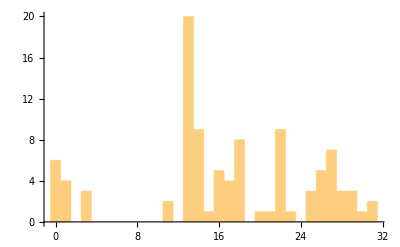

```mathematica
primergrupohisto=Histogram[Table[cifradonume[[k]],{k,1,Length[cifradonume],4}],{1}]
```

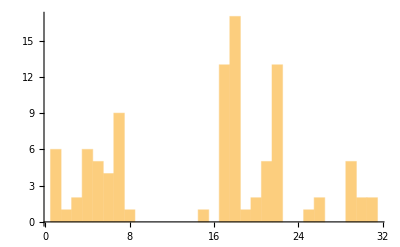

```mathematica
segundogrupohisto=Histogram[Table[cifradonume[[k]],{k,2,Length[cifradonume],4}],{1}]
```

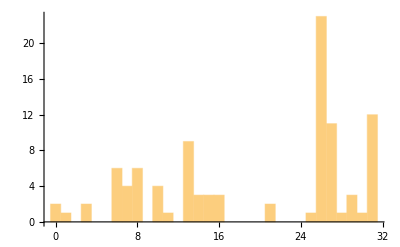

```mathematica
tercergrupohisto=Histogram[Table[cifradonume[[k]],{k,3,Length[cifradonume],4}],{1}]
```

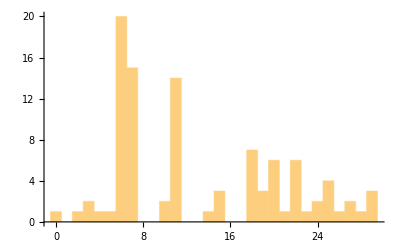

```mathematica
cuartogrupohisto=Histogram[Table[cifradonume[[k]],{k,4,Length[cifradonume],4}],{1}]
```

Para analizar los histogramas debemos compararlos con el histograma que representa la frecuencia relativa de aparición de letras en el alfabeto español:

Teniendo en cuenta los histogramas obtenidos, y sabiendo que en nuestro alfabeto la letra A ocupa la posición 5, podemos ver que el primer histograma ha sufrido un shift de 10/11 unidades, el segundo  de 13/14/ unidades el tercero de 23/24 unidades y el cuarto de 3/4 unidades. El criptoanálisis no es una ciencia exacta así que tenemos que admitir cierto grado de incertidumbre. Ahora hay que probar distintas claves de descifrado para lo cual vamos a implementar un sencillo programa. Empezaremos por la clave de cifrado  (10,13,23,3)

```mathematica
particion=Partition[cifradonume,4]
```

{{16,1,7,22},{13,5,31,6},{14,4,13,7},{27,20,27,6},{18,29,26,14},{22,22,13,25},{29,17,30,11},{13,7,8,7},{13,25,31,25},{22,21,27,6},{1,7,26,7},{26,1,13,6},{17,22,26,18},{14,5,26,11},{27,6,13,7},{28,18,14,6},{26,22,26,7},{0,4,27,20},{31,7,31,5},{14,7,8,24},{3,22,26,26},{18,31,15,15},{13,18,6,6},{21,18,29,11},{0,29,10,6},{31,7,31,6},{25,18,26,29},{22,21,27,6},{26,22,26,7},{0,4,27,20},{16,18,28,7},{13,20,10,20},{13,22,6,3},{13,21,31,18},{13,18,6,27},{14,4,26,24},{3,22,26,18},{18,17,27,18},{16,22,26,11},{27,17,31,18},{13,18,6,19},{14,17,7,15},{14,17,6,7},{13,8,10,18},{3,31,15,7},{17,17,14,28},{13,26,7,7},{20,22,8,6},{14,4,13,22},{23,1,25,0},{13,29,27,6},{25,7,21,6},{17,22,26,18},{14,17,0,11},{13,3,16,11},{13,22,8,6},{18,29,6,7},{13,18,13,10},{22,18,26,7},{27,6,31,6},{18,29,26,7},{0,18,26,10},{18,5,3,11},{0,6,27,6},{1,22,26,7},{30,18,1,22},{11,18,16,20},{13,2,27,25},{14,17,29,22},{26,19,27,27},{22,4,26,19},{22,17,0,15},{0,30,31,6},{18,30,11,11},{28,1,26,29},{22,22,8,11},{13,18,26,19},{22,17,7,11},{27,6,31,6},{1,7,26,29},{22,5,3,22},{27,17,15,11},{27,18,21,4},{11,15,26,2},{16,7,27,20},{17,1,26,23},{29,21,13,11},{13,21,10,25},{26,26,13,6},{16,1,8,6},{18,5,31,6},{1,7,31,21},{29,17,31,20},{13,3,16,11},{13,18,29,7},{15,18,26,11},{25,17,14,22},{28,18,13,3}}

```mathematica
desencrip=Flatten[Table[Mod[particion[[i]]-{10,14,23,3},32],{i,1,Length[particion]}]]
```

{6,19,16,19,3,23,8,3,4,22,22,4,17,6,4,3,8,15,3,11,12,8,22,22,19,3,7,8,3,25,17,4,3,11,8,22,12,7,4,3,23,25,3,4,16,19,22,3,7,8,3,15,4,23,3,8,17,24,22,4,18,4,23,3,16,8,3,4,22,22,4,17,21,25,8,2,4,25,17,21,25,8,3,23,8,17,24,12,3,4,15,3,11,4,6,8,22,15,19,3,21,25,8,3,15,4,3,26,12,7,4,3,16,8,3,4,22,22,4,17,6,4,5,4,3,6,19,17,3,8,15,0,3,7,8,15,3,4,15,24,4,22,3,21,25,8,3,15,8,3,4,15,6,8,3,8,17,3,8,15,3,4,15,16,4,3,16,12,4,3,15,4,3,26,19,15,25,17,24,4,7,3,23,25,3,12,16,4,10,8,17,3,4,22,22,19,13,19,2,29,3,15,4,3,15,25,30,3,7,8,3,15,4,3,9,8,3,21,25,8,3,8,17,3,8,15,15,4,3,4,22,7,12,4,3,4,17,24,8,3,8,15,3,4,22,4,3,7,8,23,12,8,22,24,4,3,23,8,3,4,20,4,10,19,1,4,25,17,3,20,4,22,4,3,6,19,16,5,4,24,12,22,3,16,12,3,9,12,22,16,8,3,8,16,20,8,18,19,3,26,12,8,17,8,3,4,3,16,12,3,16,8,17,24,8,3,23,25,3,26,12,23,12,19,17,3,24,8,17,4,30,1,1,1,3,31,6,25,4,17,7,19,3,20,19,7,22,8,3,7,19,22,16,12,22,3,6,19,17,3,8,23,8,3,23,25,8,18,19,3,8,17,3,21,25,8,3,4,6,4,5,4,3,8,15,3,23,19,18,4,22,0}

```mathematica
desencriptacion=Table[StringTake[alf,{desencrip[[i]]+1}],{i,1,Length[desencrip]}]
```

{C,O,M,O, ,S,E, ,A,R,R,A,N,C,A, ,E,L, ,H,I,E,R,R,O, ,D,E, ,U,N,A, ,H,E,R,I,D,A, ,S,U, ,A,M,O,R, ,D,E, ,L,A,S, ,E,N,T,R,A,Ñ,A,S, ,M,E, ,A,R,R,A,N,Q,U,E,,,A,U,N,Q,U,E, ,S,E,N,T,I, ,A,L, ,H,A,C,E,R,L,O, ,Q,U,E, ,L,A, ,V,I,D,A, ,M,E, ,A,R,R,A,N,C,A,B,A, ,C,O,N, ,E,L,!, ,D,E,L, ,A,L,T,A,R, ,Q,U,E, ,L,E, ,A,L,C,E, ,E,N, ,E,L, ,A,L,M,A, ,M,I,A, ,L,A, ,V,O,L,U,N,T,A,D, ,S,U, ,I,M,A,G,E,N, ,A,R,R,O,J,O,,,Y, ,L,A, ,L,U,Z, ,D,E, ,L,A, ,F,E, ,Q,U,E, ,E,N, ,E,L,L,A, ,A,R,D,I,A, ,A,N,T,E, ,E,L, ,A,R,A, ,D,E,S,I,E,R,T,A, ,S,E, ,A,P,A,G,O,.,A,U,N, ,P,A,R,A, ,C,O,M,B,A,T,I,R, ,M,I, ,F,I,R,M,E, ,E,M,P,E,Ñ,O, ,V,I,E,N,E, ,A, ,M,I, ,M,E,N,T,E, ,S,U, ,V,I,S,I,O,N, ,T,E,N,A,Z,.,.,., ,¡,C,U,A,N,D,O, ,P,O,D,R,E, ,D,O,R,M,I,R, ,C,O,N, ,E,S,E, ,S,U,E,Ñ,O, ,E,N, ,Q,U,E, ,A,C,A,B,A, ,E,L, ,S,O,Ñ,A,R,!}

```mathematica
StringJoin[%]
```

COMO SE ARRANCA EL HIERRO DE UNA HERIDA SU AMOR DE LAS ENTRAÑAS ME ARRANQUE,AUNQUE SENTI AL HACERLO QUE LA VIDA ME ARRANCABA CON EL! DEL ALTAR QUE LE ALCE EN EL ALMA MIA LA VOLUNTAD SU IMAGEN ARROJO,Y LA LUZ DE LA FE QUE EN ELLA ARDIA ANTE EL ARA DESIERTA SE APAGO.AUN PARA COMBATIR MI FIRME EMPEÑO VIENE A MI MENTE SU VISION TENAZ... ¡CUANDO PODRE DORMIR CON ESE SUEÑO EN QUE ACABA EL SOÑAR!

En este caso hemos conseguido desencriptar el mensaje, en otra situación deberíamos haber seguido probando claves de cifrado.